# Quantum Circuit

This  is  a demonstration material accompanying the corresponding YouTube video.

## Input

```mathematica
Let[Qubit,S]
```

```mathematica
qc=QuantumCircuit[Ket[S@{1,2}]]
```

```mathematica
Elaborate[qc]
```

## Single-Qubit Operators

```mathematica
qc=QuantumCircuit[S[1,1]]
```

```mathematica
qc=QuantumCircuit[S[1,6],S[2,6]]
```

```mathematica
qc=QuantumCircuit[{S[1,6],S[2,6]}]
```

```mathematica
qc=QuantumCircuit[S[{1,2},6]]
```

```mathematica
op=Elaborate[qc]
```

```mathematica
S[1,6]**S[2,6]
```

```mathematica
mat=Matrix[qc];
MatrixForm[mat]
```

```mathematica
out=qc**Ket[]
```

```mathematica
Basis[S@{1,2}]
```

## Two-Qubit Operators

### CNOT (Controlled-NOT)

```mathematica
qc=QuantumCircuit[CNOT[S[1],S[2]]]
```

```mathematica
in=Basis[S@{1,2}]
```

```mathematica
out=qc**in
```

```mathematica
Thread[in->out]//TableForm
```

```mathematica
Matrix[qc]//MatrixForm
```

## Measurements

```mathematica
qc=QuantumCircuit[Ket[S@{1,2,3}],
S[1,6],CNOT[S[1],S[2]],CNOT[S[1],S[3]],"Separator",
Measurement[S[1,3]],Measurement[S[2,3]]]
```

```mathematica
out=Elaborate[qc]
```

```mathematica
data=Table[Elaborate[qc];Readout[S[{1,2},3]],10]
```

```mathematica
Histogram3D[data]
```

```mathematica
qc=QuantumCircuit[Ket[S@{1,2,3}],
S[1,6],CNOT[S[1],S[2]],CNOT[S[1],S[3]],"Separator",
Measurement[S[{1,2},3]]]
```

```mathematica
data=Table[Elaborate[qc];Readout[S[{1,2},3]],10]
```

```mathematica
Histogram3D[data]
```

## List vs Sequence

We want to generate the following quantum circuit for different numbers of target qubits.

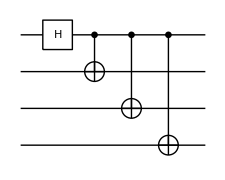

What should we do?

```mathematica
Let[Qubit,S,T]
```

```mathematica
$n=3;
TT=T[Range[$n],$]
```

```mathematica
cn=Table[CNOT[S[1],q],{q,TT}];
cn//TableForm
```

```mathematica
qc=QuantumCircuit[S[1,6],cn]
```

```mathematica
cn
```

```mathematica
QuantumCircuit[S[1,6],CNOT[S[1],T[1]],CNOT[S[1],T[2]],CNOT[S[1],T[3]]]
```

Is there any simpler way?

```mathematica
qc=QuantumCircuit[S[1,6],Sequence@@cn]
```

List, Sequence, and @@.

## Summary

### Functions

QuantumCircuit

Elaborate, ExpressionFor

Matrix, MatrixForm

Apply

### Related Links

Chapter 2 of the Quantum Workbook (2022, 2023).

Tutorial: “Quantum Computation: Overview”

Full List of Demonstrations in YouTube Videos